# POLINOMIOS DE HERMITE

Queremos Interpolar f(x_k)=P(x_k) y adicionalmente conservar la inclinación f'(x_k)=P'(x_k).

### TEOREMA

#### Si f∈C^1[a,b] y x_0,... ,x_n∈[a,b] son distintos, el único polinomio de menor grado que coincide con f y f’ en x_0,...,x_n es el polinomio de Hermite de grado a lo mas 2n+1, dado por:

#### PH_(2n+1)(x)=∑_(j=0)^n f(x_j)H_j(x)+∑_(j=0)^n f'(x_j)(Ĥ)_j(x)

#### donde

#### H_j(x) = (1 - 2 (x - x_j) L_j^1(x_j))L_j^2(x) (Ĥ)_j(x)=(x-x_j)L_j^2(x)

#### Además, si f∈C^(2n+2)[a,b], entonces:

#### f(x)=PH_(2n+1)(x)+((x-x_0)^2···(x-x_n)^2)/((2n+2)!)f^(2n+2)(ξ(x))

```mathematica
A={{"k","x_k","f(x_k)","f'(x_k)"},{0,0,0,1/2-1/100},{1,2,11/10-1/9,1/2-1/64},{2,5,26/10-1/5,1/2-1/25},{3,9,46/10-1,-1/2},{4,9.5,48.5/10-2,-7/2}}//TableForm
```

k | x_k | f(x_k) | f'(x_k)
0 | 0 | 0 | 49/100
1 | 2 | 89/90 | 31/64
2 | 5 | 12/5 | 23/50
3 | 9 | 18/5 | -1/2
4 | 9.5 | 2.85 | -7/2

Esperamos que el polinomio de Hermite para estos datos sea de grado 5.

#### 1er Paso: Calcular polinomios de Lagrange

```mathematica
Subscript[L, 0][x_]:=((x-2)(x-5)(x-9)(x-9.5))/((-2)(-5)(-9)(-9.5))
```

```mathematica
Subscript[L, 1][x_]:=((x)(x-5)(x-9)(x-9.5))/((2-5)(2-9)(2-9.5)(2-0))
```

```mathematica
Subscript[L, 2][x_]:=((x-0)(x-9)(x-9.5)(x-2))/((5-2)(5-0)(5-9)(5-9.5))
```

```mathematica
Subscript[L, 3][x_]:=((x-0)(x-9.5)(x-5)(x-2))/((9-2)(9-0)(9-5)(9-9.5))
```

```mathematica
Subscript[L, 4][x_]:=((x-0)(x-9)(x-5)(x-2))/((9.5-2)(9.5-0)(9.5-9)(9.5-5))
```

#### 2do Paso: Calcular derivada de Lagrange en los puntos x_k

```mathematica
L0:=N[Subscript[L, 0]'[0]]
```

```mathematica
L1:=N[Subscript[L, 1]'[2]]
```

```mathematica
L2:=N[Subscript[L, 2]'[5]]
L3:=N[Subscript[L, 3]'[9]]
```

```mathematica
L4:=N[Subscript[L, 4]'[9.5]]
```

#### 3er Paso: Calcular los H_k(x)

```mathematica
Subscript[H, 0][x_]:=(1-2(x-0)L0)(Subscript[L, 0][x])^2
```

```mathematica
Subscript[H, 1][x_]:=(1-2(x-2)L1)(Subscript[L, 1][x])^2
```

```mathematica
Subscript[H, 2][x_]:=(1-2(x-5)L2)(Subscript[L, 2][x])^2
```

```mathematica
Subscript[H, 3][x_]:=(1-2(x-9)L3)(Subscript[L, 3][x])^2
```

```mathematica
Subscript[H, 4][x_]:=(1-2(x-9.5)L4)(Subscript[L, 4][x])^2
```

#### 4to Paso: Calcular los (Ĥ)_k(x)

```mathematica
Subscript[Ha, 0][x_]:=(x-0)(Subscript[L, 0][x])^2
```

```mathematica
Subscript[Ha, 1][x_]:=(x-2)(Subscript[L, 1][x])^2
```

```mathematica
Subscript[Ha, 2][x_]:=(x-5)(Subscript[L, 2][x])^2
```

```mathematica
Subscript[Ha, 3][x_]:=(x-9)(Subscript[L, 3][x])^2
```

```mathematica
Subscript[Ha, 4][x_]:=(x-9.5)(Subscript[L, 4][x])^2
```

#### 5to Paso: Felicidad

```mathematica
Subscript[PH, 5][x_]:=0*Subscript[H, 0][x]+89/90*Subscript[H, 1][x]+12/5*Subscript[H, 2][x]+18/5*Subscript[H, 3][x]+2.85*Subscript[H, 4][x]+49/100*Subscript[Ha, 0][x]+31/64*Subscript[Ha, 1][x]+23/50*Subscript[Ha, 2][x]-1/2*Subscript[Ha, 3][x]-7/2*Subscript[Ha, 4][x]
```

```mathematica
Expand[Subscript[PH, 5][x]]
L[x_]:=0*Subscript[L, 0][x]+89/90*Subscript[L, 1][x]+12/5*Subscript[L, 2][x]+18/5*Subscript[L, 3][x]+2.85*Subscript[L, 4][x]
```

0.+0.49 x+1.84094 x^2-3.17317 x^3+2.17928 x^4-0.7716 x^5+0.153276 x^6-0.0172321 x^7+0.00102364 x^8-0.0000249693 x^9

```mathematica
Expand[L[x]]
```

0.+0.936349 x-0.357848 x^2+0.0785362 x^3-0.00504409 x^4

```mathematica
Subscript[PH, 5]'[x]
```

6.70292×10^-7 (-9.5+x)^2 (-9+x)^2 (-5+x)^2 (-2+x)^2+0.0000199323 (1+0.219048 (-2+x)) (-9.5+x)^2 (-9+x)^2 (-5+x)^2 x+0.0000111037 (-9.5+x)^2 (-9+x)^2 (-5+x)^2 (-2+x) x+0.0000658436 (1-0.122222 (-5+x)) (-9.5+x)^2 (-9+x)^2 (-2+x)^2 x+0.0000139606 (-9.5+x)^2 (-9+x)^2 (-5+x) (-2+x)^2 x+0.000453515 (1+2.99206 (-9+x)) (-9.5+x)^2 (-5+x)^2 (-2+x)^2 x-0.0000616476 (-9.5+x)^2 (-9+x) (-5+x)^2 (-2+x)^2 x+0.000221789 (1-4.92164 (-9.5+x)) (-9+x)^2 (-5+x)^2 (-2+x)^2 x-0.000271032 (-9.5+x) (-9+x)^2 (-5+x)^2 (-2+x)^2 x+0.0000199323 (1+0.219048 (-2+x)) (-9.5+x)^2 (-9+x)^2 (-5+x) x^2+0.0000199323 (1+0.219048 (-2+x)) (-9.5+x)^2 (-9+x) (-5+x)^2 x^2+0.0000199323 (1+0.219048 (-2+x)) (-9.5+x) (-9+x)^2 (-5+x)^2 x^2+7.06464×10^-6 (-9.5+x)^2 (-9+x)^2 (-5+x)^2 x^2+0.0000658436 (1-0.122222 (-5+x)) (-9.5+x)^2 (-9+x)^2 (-2+x) x^2+0.0000223832 (-9.5+x)^2 (-9+x)^2 (-5+x) (-2+x) x^2+0.000453515 (1+2.99206 (-9+x)) (-9.5+x)^2 (-5+x)^2 (-2+x) x^2-0.000053225 (-9.5+x)^2 (-9+x) (-5+x)^2 (-2+x) x^2+0.000221789 (1-4.92164 (-9.5+x)) (-9+x)^2 (-5+x)^2 (-2+x) x^2-0.000262609 (-9.5+x) (-9+x)^2 (-5+x)^2 (-2+x) x^2+0.0000658436 (1-0.122222 (-5+x)) (-9.5+x)^2 (-9+x) (-2+x)^2 x^2+0.0000658436 (1-0.122222 (-5+x)) (-9.5+x) (-9+x)^2 (-2+x)^2 x^2+2.28624×10^-6 (-9.5+x)^2 (-9+x)^2 (-2+x)^2 x^2+0.000453515 (1+2.99206 (-9+x)) (-9.5+x)^2 (-5+x) (-2+x)^2 x^2-0.0000503681 (-9.5+x)^2 (-9+x) (-5+x) (-2+x)^2 x^2+0.000221789 (1-4.92164 (-9.5+x)) (-9+x)^2 (-5+x) (-2+x)^2 x^2-0.000259752 (-9.5+x) (-9+x)^2 (-5+x) (-2+x)^2 x^2+0.000453515 (1+2.99206 (-9+x)) (-9.5+x) (-5+x)^2 (-2+x)^2 x^2+0.000646978 (-9.5+x)^2 (-5+x)^2 (-2+x)^2 x^2+0.000221789 (1-4.92164 (-9.5+x)) (-9+x) (-5+x)^2 (-2+x)^2 x^2-0.000335361 (-9.5+x) (-9+x) (-5+x)^2 (-2+x)^2 x^2-0.000681969 (-9+x)^2 (-5+x)^2 (-2+x)^2 x^2

```mathematica
Expand[%142]
```

0.49+3.68187 x-9.51952 x^2+8.71712 x^3-3.858 x^4+0.919657 x^5-0.120625 x^6+0.0081891 x^7-0.000224724 x^8

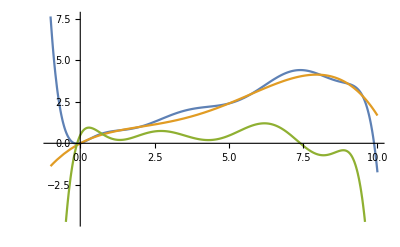

```mathematica
Plot[{Subscript[PH, 5][x],L[x],Subscript[PH, 5]'[x] },{x,-1,10}]
```

```mathematica
fig[x_]:=0.+0.49000000000000005 x+1.840936622664934 x^2-3.1731728080870747 x^3+2.1792810363318313 x^4-0.7716002347725193 x^5+0.15327621138892544 x^6-0.017232098873745078 x^7+0.0010236375894665164 x^8-0.00002496933909758305 x^9;
```

```mathematica
fig'[0]
```

0.49

```mathematica
fig'[x]
```

0.49+3.68187 x-9.51952 x^2+8.71712 x^3-3.858 x^4+0.919657 x^5-0.120625 x^6+0.0081891 x^7-0.000224724 x^8